# Exercise 2

As with all of the exercises you will complete in this course, you will be expected to turn your *.nb file in to the course TA before the next lecture.  Please do so by e-mailing your completed exercise file to Lan Yu (lanyu2@illinois.edu), make sure you name the file using the following notation: “Exn_First_Last.nb”, where n is the Exercise number (in this case, 2), and First and Last would be your first and last name.  So my submission to Lan for this exercise would be titled “Ex2_Dan_Wasserman.nb”.  You will receive full credit for your exercise if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In today’s exercise, we will look at how to construct electric fields from charge distributions.  There are two ways we can do this, the hard way or the easy way.  We will do both.

```mathematica
ClearAll[ro,rq,rhat,dE,etotal]
```

## The Electric Field From a Line of Uniform Linear Charge Density

In your previous exercse, you learned how to plot vector fields.  Today we are going to learn how to find the electric field from a linear charge distribution.  First we are going to do this by brute force (hard way).  Then we will use Gauss’s Law (easy way).  Please note that though we are using a linear and uniform charge density, we can take the basic principles we develop here and extend them to more complicated charge distributions. Here is the system we are going to be working with:
-Graphics-
The blue line is our linear charge density, which we will assume, for now, goes on to infinity in both directions.

### Brute Force

We already know how to write the Electric Field from a single point charge, this is nothing more than Coulomb’s Law.  In order to find the Electric Field from a distribution of charge, we can think of our charge distribution as nothing more than a collection of point charges.  Let’s break our line of charge into such point charges, each with a differential charge dQ=λdz, and position z, along the z axis. In order to find the Electric Field (at a point ro=(xo,yo,zo) in space) from one of these “point charges”, at position z, we need to know only the vector that separates these two points.  Because we will need to end up taking an integral, let’s write our expressions in function form:

```mathematica
ro={xo,yo,zo}
```

{xo,yo,zo}

```mathematica
rq[z_]:=ro-{0,0,z}
```

```mathematica
rhat[z_]:=rq[z]/(Sqrt[rq[z].rq[z]])
```

```mathematica
eps=8.85*^-12
```

8.85×10^-12

```mathematica
dE[z_]=(λ/(4*Pi*eps*rq[z].rq[z]))*rhat[z]
```

{(8.9918×10^9 xo λ)/((xo^2+yo^2+(-z+zo)^2)^(3/2)),(8.9918×10^9 yo λ)/((xo^2+yo^2+(-z+zo)^2)^(3/2)),(8.9918×10^9 (-z+zo) λ)/((xo^2+yo^2+(-z+zo)^2)^(3/2))}

Looks like a mess, right?  This would be a pain to solve by hand...but it it pretty easy to work with in Mathematica.
This expression gives us the differential Electric Field at {xo,yo,zo} from any point z on the wire.  Let’s see what the field is from a point on the wire “dz” above “zo”

```mathematica
dE[zo+dz]
```

{(8.9918×10^9 xo λ)/((dz^2+xo^2+yo^2)^(3/2)),(8.9918×10^9 yo λ)/((dz^2+xo^2+yo^2)^(3/2)),-(8.9918×10^9 dz λ)/((dz^2+xo^2+yo^2)^(3/2))}

What about a point “dz” below “zo”?

```mathematica
dE[zo-dz]
```

{(8.9918×10^9 xo λ)/((dz^2+xo^2+yo^2)^(3/2)),(8.9918×10^9 yo λ)/((dz^2+xo^2+yo^2)^(3/2)),(8.9918×10^9 dz λ)/((dz^2+xo^2+yo^2)^(3/2))}

What is the combined Electric field from both of these pieces of wire?:

```mathematica
dE[zo+dz]+dE[zo-dz]
```

{(1.79836×10^10 xo λ)/((dz^2+xo^2+yo^2)^(3/2)),(1.79836×10^10 yo λ)/((dz^2+xo^2+yo^2)^(3/2)),0.}

We see two things: First, the z-component of the Electric field from these two pieces cancels, and second, the field is entirely in the radial direction! We recognize this as a result of symmetry.  Anywhere in space, for an infinite wire, we will see an Electric Field that is entirely radial in nature, since the field from any line segment above our point in space will be matched by the field from a segment of equal charge, and equal distance below, as shown in the figure below:
-Graphics-
Now we are ready to determine the electric field from the entire wire.  To do this, we simply need to integrate over all of the charge that makes up the wire.  In a sense, what we are doing is adding up the differential electric fields from all of the little pieces of the wire.  Below, solve for the total electric field at a point {xo, yo, zo}, if your linear charge density is λ=2ϵ_o[C/m].  You should end up with an expression that returns the electric field at any point {x,y,z}. 
HInt: Things get tricky when Mathematica tries to solve for points along the line of charge, so you may want to insert some assumptions into your Integral, telling Mathematica that xo^2+yo^2>0 and that {xo,yo,zo} is a real number, you can do this by adding: “Assumptions→{xo∈Reals, yo∈Reals,zo∈Reals,xo^2+yo^2>0}” into your integral command.  Don’t forget to assign a value to λ.  Let’s call the integrated function “etotal”.

```mathematica
λ=2*eps;
etotal=Integrate[dE[z], {z,-Infinity,Infinity}, Assumptions->{xo∈Reals, yo∈Reals,zo∈Reals,xo^2+yo^2>0}]
```

{(0.31831 xo)/(xo^2+yo^2),(0.31831 yo)/(xo^2+yo^2),0.}

Mathematica probably performed this Integral rather quickly, let’s look and see what happens when we try to plot this vector field in 3D...

```mathematica
VectorPlot3D[etotal,{xo,-1,1},{yo,-1,1},{zo,-3,3},VectorPoints->Automatic]
```

-Graphics3D-

Cool!!  We see a Vector field pointing in the radial direction, that decays as we extend from the wire!
Just for giggles, let’s add an image of our line charge to the plot.  We will do this by assigning the 3DGraphic “Cylinder” to “p1” and our 3D VectorPlot to “p2”.  We can then plot both of these at the same time!!

```mathematica
p1=Graphics3D[Cylinder[{{0,0,-3},{0,0,3}},.05]];
p2=VectorPlot3D[etotal,{xo,-1,1},{yo,-1,1},{zo,-3,3},VectorPoints->Automatic];
```

```mathematica
Show[p1,p2,PlotRange->All]
```

-Graphics3D-

The brute force method is much more easily done in Mathematica than by hand, and with a little adjustment, you could change the code to generate the electric field from a finite wire element, or alternatively, one with non-uniform charge distribution.
To find the electric field from a finite length wire (let’s say one that extends from -1 to 1 on the z-axis, all you have to do is change your integral:

```mathematica
etotalfinite=Integrate[dE[z], {z,-1,1}, Assumptions->{xo∈Reals, yo∈Reals,zo∈Reals, If[-1≤z≤1,xo^2+yo^2>0]}]
```

{(0.159155 xo (√(xo^2+yo^2+(-1+zo)^2)+√(xo^2+yo^2+(1+zo)^2)+zo (√(xo^2+yo^2+(-1+zo)^2)-√(xo^2+yo^2+(1+zo)^2))))/((xo^2+yo^2) √((xo^2+yo^2+(-1+zo)^2) (xo^2+yo^2+(1+zo)^2))),(0.159155 yo (√(xo^2+yo^2+(-1+zo)^2)+√(xo^2+yo^2+(1+zo)^2)+zo (√(xo^2+yo^2+(-1+zo)^2)-√(xo^2+yo^2+(1+zo)^2))))/((xo^2+yo^2) √((xo^2+yo^2+(-1+zo)^2) (xo^2+yo^2+(1+zo)^2))),(0.159155 zo (√(xo^2+yo^2+(-1+zo)^2)+√(xo^2+yo^2+(1+zo)^2)+zo (√(xo^2+yo^2+(-1+zo)^2)-√(xo^2+yo^2+(1+zo)^2))))/((xo^2+yo^2) √((xo^2+yo^2+(-1+zo)^2) (xo^2+yo^2+(1+zo)^2)))-(0.159155 ((-xo^2-yo^2+zo-zo^2+√((xo^2+yo^2+(-1+zo)^2) (xo^2+yo^2+zo^2)))/(√(xo^2+yo^2+(-1+zo)^2))+(xo^2+yo^2+zo+zo^2-√((xo^2+yo^2+zo^2) (xo^2+yo^2+(1+zo)^2)))/(√(xo^2+yo^2+(1+zo)^2))))/(xo^2+yo^2)}

```mathematica
VectorPlot3D[etotalfinite,{xo,-1,1},{yo,-1,1},{zo,-3,3},VectorPoints->Automatic]
```

-Graphics3D-

```mathematica
p1=Graphics3D[Cylinder[{{0,0,-1},{0,0,1}},.05]];
p2=VectorPlot3D[etotalfinite,{xo,-1,1},{yo,-1,1},{zo,-3,3},VectorPoints->Automatic];
```

```mathematica
Show[p1,p2,PlotRange->All]
```

-Graphics3D-

This is amazing!!  Solving this by hand would be absolutely brutal!!  But we can do it in a matter of seconds using Mathematica.

### Gauss’s Law

OK, so now let’s solve for the infitnite wire using Gauss’s Law.  As always, when using Gauss’s Law we need to think about symmetry.  For an infinite wire, we clearly have cylindrical symmetry. So we should make our Gaussian surface a cylinder.  We recongnize, as we did above, that the Electric field at the surface of the cylinder will NOT depend on z or θ, and that the field will always be pointing in the radial direction.

We can write the total charge enclosed as:

```mathematica
qlnenc=λo*L
```

L λo

And we can write the flux through our cylindrical surface, assuming the field is only in the r direction and therefore parallel to the top and bottom of our cylinder, as:

```mathematica
ecylflux=efieldgl*2*Pi*Rr*L
```

2 efieldgl L π Rr

```mathematica
Solve[ecylflux*eps==qlnenc,efieldgl]
```

{{efieldgl→(1.79836×10^10 λo)/Rr}}

We can write this in equation form

```mathematica
λo=2*eps;
```

```mathematica
elinegl[r1_,theta1_,z1_]:={λo/(2*Pi*eps*r1),0,0}
```

But unfortunately, there is no good way to generate a 3D vector plot from an expression in cylindrical coordinates.  So we can transform the expression in clylindrical coordinates to cartesian coordinates

```mathematica
elineglxyz=TransformedField["Cylindrical"->"Cartesian", elinegl[r1,theta1,zc],{r1,theta1,zc}->{x1,y1,z1}]
```

{(0.31831 x1)/(x1^2+y1^2),(0.31831 y1)/(x1^2+y1^2),0.}

```mathematica
VectorPlot3D[elineglxyz, {x1,-2,2}, {y1,-2,2}, {z1,-3,3}]
```

-Graphics3D-

Cool!  Now it’s your turn.  Use Gauss’s Law to determine the Electric Field for a sphere of Radius R and uniform charge density ρ_o.  First solve for the electric field in spherical coordinates symbolically.  Then use this to write and expression for the electric field from a charged sphere of radius R=1m and ρ_o=-2ϵ_o.  Then plot in VectorPlot3D, after transforming to cartesian coordinates.

We have to consider the solution in 2 regions, the first for when r<R, the second for when r>R.  Using Gauss’s Law:
E⃗(r<R)=-r/3, E⃗(r>R)=-R^3/(3 r^2)

```mathematica
esphere[rs_]:=If[rs<1,{-rs/3,0,0},{-1/(3*rs^2),0,0}]
```

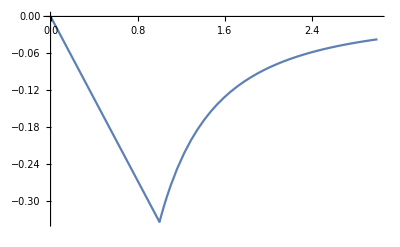

```mathematica
Plot[esphere[rs][[1]],{rs,0,3}]
```

```mathematica
espherexyz1=TransformedField["Spherical"->"Cartesian", {-rs/3,0,0},{rs,theta,phi}->{x,y,z}]
```

{-x/3,-y/3,-z/3}

```mathematica
espherexyz2=TransformedField["Spherical"->"Cartesian", {-1/(3*rs^2),0,0},{rs,theta,phi}->{x,y,z}]
```

{-x/(3 (x^2+y^2+z^2)^(3/2)),-y/(3 (x^2+y^2+z^2)^(3/2)),-z/(3 (x^2+y^2+z^2)^(3/2))}

```mathematica
espherexyz=If[Sqrt[x^2+y^2+z^2]<1, espherexyz1, espherexyz2]
```

If[√(x^2+y^2+z^2)<1,espherexyz1,espherexyz2]

```mathematica
VectorPlot3D[espherexyz,{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-